## Brian — PS 19 — 2025-04-18 — Solution

## EIWL3 Sections 43 and 44

## Exercises from EIWL3 Section 43

```mathematica
(* There were no excercises for Section 43, so I did some simple experimentation: *)
bin=CreateDatabin[]
```

Databin[…]

```mathematica
DatabinAdd[bin,{1,2}]
```

Databin[…]

```mathematica
DatabinAdd[bin,{3,4}]
```

Databin[…]

```mathematica
Values[bin]
```

{{1,2},{3,4}}

```mathematica
cloudObject=CloudPut[Entity["TaxonomicSpecies","VulpesVulpes::48y38"]["Image"]]
```

CloudObject[https://www.wolframcloud.com/obj/ad9e966b-cd8b-40a5-b6e4-18bedf947eed]

```mathematica
CloudGet[cloudObject]
```

-Graphics-

## Exercises from EIWL3 Section 44

```mathematica
(* 44.1 *) WebImageSearch["https://www.google.com"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 44.2 *) dominantColors = DominantColors/@WebImageSearch["https://www.google.com"];
```

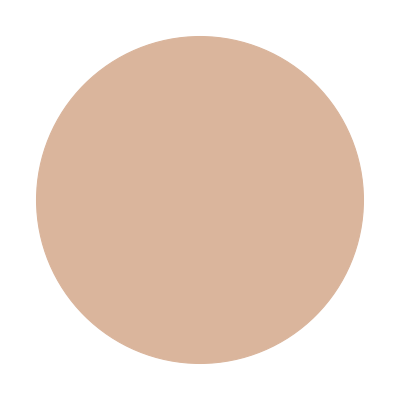
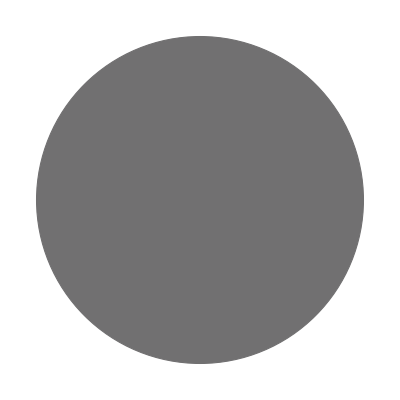
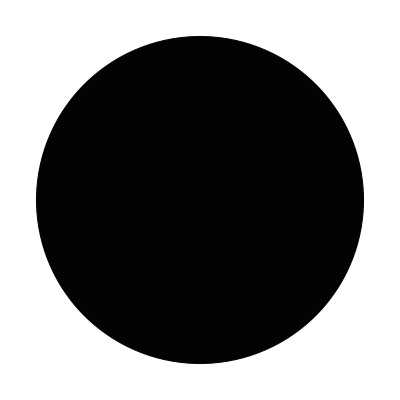
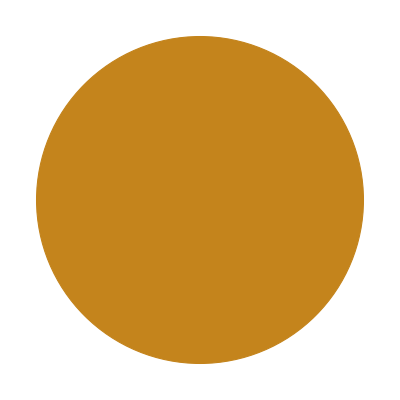
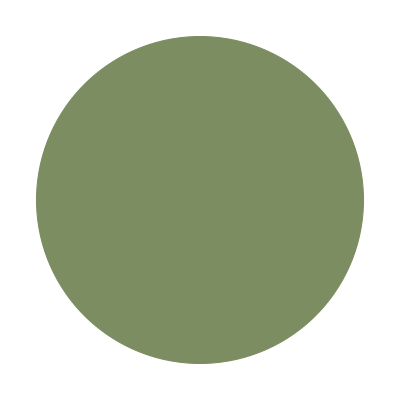
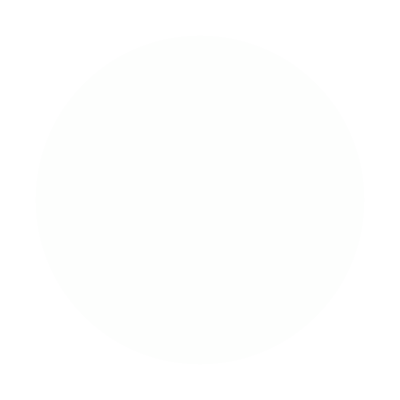
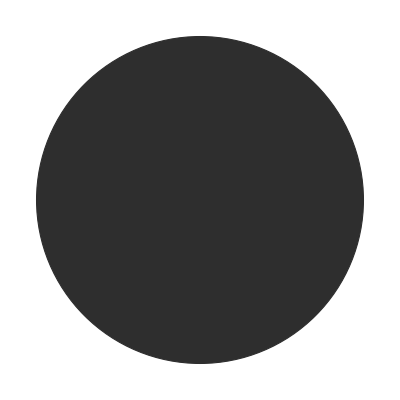
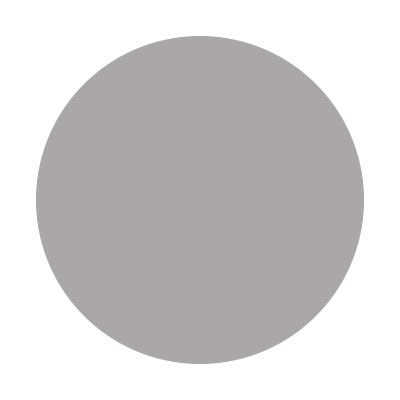
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |

```mathematica
(* I prettified the output a little with EdgeForm[] and Grid[]: *)
Map[Graphics[{#,EdgeForm[Thick],Disk[]}]&,dominantColors,{2}]//Grid
```

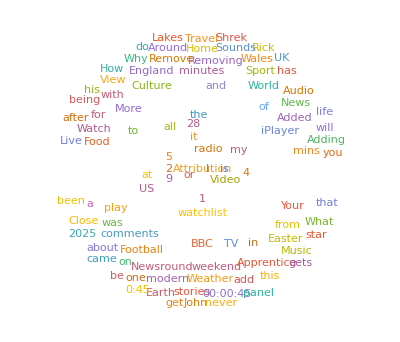

```mathematica
(* 44.3 *) bbcText=Import["https://bbc.co.uk"];
WordCloud[TextWords[bbcText]]
```

```mathematica
(* 44.4 *) npsImages=Import["https://nps.gov","Images"];
ImageCollage[npsImages]
```

-Graphics-

```mathematica
(* 44.5 *) ostrichPageImages=Import["https://en.wikipedia.org/wiki/Ostrich","Images"];
Select[ostrichPageImages,ImageInstanceQ[#,"bird"]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 44.6 *) natoTextWords=TextWords[Import["https://en.wikipedia.org/wiki/NATO"]];
(* Programmatic access to nato.int is blocked, so I switched to the Wikipedia. *)
Flatten[TextCases[natoTextWords,"Country"]]
(* Also, I don't understand why I am getting all these empty lists along with the countries *)
```

{Bosnia,Herzegovina,Kosovo,Afghanistan,Iraq,Libya,Turkish,Deutsch,Fiji,Français,Indonesia,Nederlands,Belgium,Albania,Belgium,Bulgaria,Canada,Croatia,Czech,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Italy,Latvia,Lithuania,Luxembourg,Montenegro,Netherlands,Macedonia,Norway,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden,Turkey,US,US,US,American,Belgium,Belgium,Sweden,Bosnia,Herzegovina,Georgia,Ukraine,Russia,France,Germany,America,Canada,Portugal,Italy,Norway,Denmark,Iceland,Canadian,Germany,Korean,Greece,Turkey,Germany,US,France,Spain,Germany,Germany,Bosnia,Russia,Hungary,Poland,Czech,Afghanistan,Iraq,France,France,S,Russian,Crimea,Iraq,Syrian,Estonia,Latvia,Lithuania,Poland,Russian,Ukraine,Bulgaria,Hungary,Romania,Slovakia,Russian,Bulgaria,Romania,Hungary,Slovakia,Poland,Bulgaria,Spain,Netherlands,US,Iraqi,Kuwait,Turkey,Bosnia,Herzegovina,Bosnia,Herzegovina,Bosnian,Bosnia,Herzegovina,Bosnian,Serb,Bosnian,Serb,US,Serbs,Serb,Kosovo,Kosovo,Kosovo,Serbian,Albanian,Kosovo,US,Albania,Albania,Kosovo,Chinese,US,UK,Serbia,France,US,UK,Russia,China,Kosovo,Kosovo,Albanian,Macedonia,Afghanistan,Afghanistan,Germany,Netherlands,S,Afghanistan,Afghan,Afghanistan,Afghanistan,US,France,Afghanistan,Afghanistan,Afghan,Afghan,Afghanistan,Afghanistan,Afghan,Iraq,Iraq,S,Iraq,Iraq,Iraqi,US,Iraqi,Iraqi,Iraq,Iraqi,US,Turkey,Iraq,Turkey,Syrian,Turkish,Turkey,Syria,Iraq,Somalia,Russia,China,Korea,Indian,Libya,Libya,Libyan,Libyan,Libyan,Libya,Libya,Qatar,US,Poland,Spain,Netherlands,Turkey,Germany,Norway,Libyan,Turkish,S,Turkey,Turkey,Syrian,Turkish,Turkish,Syrian,Turkish,Syria,Syrian,Turkish,Turkey,Turkey,Syria,Syrian,Russian,Turkish,Russia,Albania,Belgium,Bulgaria,Canada,Croatia,Czech,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Italy,Latvia,Lithuania,Luxembourg,Montenegro,Netherlands,Macedonia,Norway,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden,Turkey,Albania,Belgium,Bulgaria,Canada,Croatia,Czech,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Italy,Latvia,Lithuania,Luxembourg,Montenegro,Netherlands,Macedonia,Norway,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden,Turkey,Bosnia-Herzegovina,Australia,Georgia,Jordan,Ukraine,Armenia,Azerbaijan,Bosnia-Herzegovina,Georgia,Kazakhstan,Moldova,Serbia,Ukraine,Armenia,Austria,Azerbaijan,Belarus,Bosnia-Herzegovina,Georgia,Ireland,Kazakhstan,Kyrgyzstan,Malta,Moldova,Russia,Serbia,Switzerland,Tajikistan,Turkmenistan,Ukraine,Uzbekistan,Algeria,Egypt,Israel,Jordan,Mauritania,Morocco,Tunisia,Bahrain,Kuwait,Qatar,Australia,Colombia,Iraq,Japan,Mongolia,Pakistan,Korea,America,America,Turkey,Belgian,Congo,Algeria,Nordic,Denmark,Iceland,Norway,Denmark,S,Greenland,France,France,France,Belgium,Canada,Denmark,France,Iceland,Italy,Luxembourg,Netherlands,Norway,Portugal,Greece,Turkey,Germany,Spain,Germany,Germany,Hungary,Poland,Czech,Bulgaria,Estonia,Latvia,Lithuania,Romania,Slovakia,Slovenia,Albania,Croatia,Montenegro,Macedonia,Finland,Sweden,Russia,Ukraine,Ukraine,Ukraine,Ukraine,Russia,Crimea,Ukraine,Ukraine,Ukraine,Ukraine,Russian,Ukraine,Russian,Ukraine,Ukraine,Ukraine,Russian,Ukraine,Ukraine,Russia,Russia,Russia,Russia,Russia,Ukraine,Russia,Ukraine,Ukraine,Russia,Georgia,US,Russia,Ukraine,Finland,Russia,US,Russians,Poland,Russia,Russia,Poles,Russia,Poles,US,Poland,Serbia,Montenegro,China,Germany,Canada,Jordan,Afghanistan,EU,EU,EU,Israel,Qatar,Qatar,Japan,Australia,China,Australia,Japan,Korea,Colombia,American,France,France,Iraqi,Australia,Australia,Greece,Turkey,Russia,Australia,Canada,American,Britain,Luxembourg,Canada,Germany,France,Spain,US,S,Ukraine,US,Kosovo,Macedonia,UK,S,S,Poland,Ukraine,Spain,Spain,Bulgaria,EU,Russia,Deutsche,Serbs,Kosovo,Kosovo,Kosovo,Kosovo,Macedonia,Kosovo,Afghanistan,Afghanistan,Afghanistan,France,France,Afghan,Afghanistan,Afghanistan,US,Afghanistan,Afghanistan,EU,Deutsche,Afghanistan,Deutsche,Afghanistan,Iraq,Syria,Turkey,Turkey,Syrian,Libya,Libya,Libya,Canadian,Libya,Libya,UAE,Qatar,Libya,Malaysia,Libya,US,Libya,Norway,Libya,Malta,Libya,Britain,Libya,Libya,Libya,USA,Libya,Libya,Turkey,Syrian,Syria,Turkey,Syria,Turkey,Turkey,Syrian,Turkey,S,Syria,Russia,Turkish,Greece,Turkey,Syria,Russian,Syrian,Syrian,Turkish,Denmark,Macedonia,Russia,Finland,Ukraine,Ukraine,France,Ukraine,Ukraine,EU,EU,Russia,Ukraine,Russian,Ukraine,Russia,Ukraine,Russia,Ukraine,Russia,Russia,Ukraine,US,Russia,Ukraine,Ukraine,Russia,Georgia,Russian,American,Russia,Poland,Turkey,Poland,USA,Deutsche,China,Russia,America,Ukraine,Georgia,Belarus,Afghanistan,Netherlands,Qatar,Qatar,Qatar,S,China,Colombia,Colombia,American,France,EU,S,Ukraine,US,Korea,Vietnam,Afghanistan,Iraq,US,US,Italy,Denmark,France,Germany,Netherlands,Greece,Poland,Lithuania,Romania,Britain,US,Germany,Italy,Belgium,Netherlands,US,US,US,Norfolk,Albania,Belgium,Bulgaria,Canada,Croatia,Czech,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Italy,Latvia,Lithuania,Luxembourg,Montenegro,Netherlands,Macedonia,Norway,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden,Turkey,Russia,Jamaican,Korea,Indonesian,Iran,Greek,Turkish,Germany,Indochina,Polish,India,Pakistani,Palestine,Palestine,Israeli,Palestinian,Chinese,Chinese,Syrian,Korean,Egyptian,Iraqi,Iranian,Syrian,Guatemalan,Taiwan,Algerian,Kashmir,Vietnam,Cyprus,Polish,Syrian,Iraqi,Lebanon,Taiwan,Cuban,Cuban,Congo,Turkish,Albanian,Albania,Iraqi,Iraqi,Indonesia,Malaysia,Portuguese,Angolan,Guinea-Bissau,Mozambican,Cuban,Indian,Eritrean,Yemen,Syrian,Cyprus,Mexican,Guatemalan,Colombian,Brazilian,Dominican,Indonesian,Indonesia,Syrian,Argentine,Korean,Greek,Italy,Nigerian,Polish,Malaysia,Peruvian,Sudanese,Libyan,Syria,Cambodian,Thailand,Polish,Egypt,Turkish,Sudanese,Bolivian,Bangladesh,China,Yemen,Yemen,Yemenite,Bangladesh,Eritrean,Uruguayan,Afghan,Chilean,Iraqi,Turkish,Cyprus,Bangladeshi,Angolan,Cambodian,Mozambican,Ethiopian,Lebanese,Albanian,Indochina,Cambodian,Vietnamese,Cambodian,Argentina,Argentine,Egyptian,Libyan,Korean,Nicaraguan,Uganda,Tanzania,Chadian,Libyan,Yemenite,Iranian,Vietnamese,Salvadoran,Afghan,Peruvian,Eritrean,Turkish,Ugandan,Poland,Falklands,Ethiopian,Grenada,Iran,Iraq,Yemen,American,Korean,Afghan,Panama,Polish,Polish,Romanian,Mongolian,Yemeni,Albania,China,Taiwan,Korea,Kosovo,Indian,American,Deutschland,America,Russian,American,Russian,Russian,Russia,Russian,S,Rican,Japan,S,Korean,S,S,Afghanistan,Iraq,Afghanistan,Iraq,Iraqi,Pakistan,Philippines,Ethiopia,Uzbekistan,Afghanistan,Philippines,Georgia,Georgia,Pakistan,Philippines,Iraq,Iraqi,Saudi,Arabia,Somalia,Lebanon,Yemen,America,Iranian,Korea,Albania,Armenia,Austria,Azerbaijan,Belarus,Belgium,Bosnia,Herzegovina,Bulgaria,Croatia,Cyprus,Czech,Denmark,Estonia,Finland,France,Georgia,Germany,Greece,Hungary,Iceland,Ireland,Italy,Kazakhstan,Latvia,Lithuania,Luxembourg,Malta,Moldova,Monaco,Montenegro,Netherlands,Macedonia,Norway,Poland,Portugal,Romania,Russia,Marino,Serbia,Slovakia,Slovenia,Spain,Sweden,Switzerland,Turkey,Ukraine,Vatican,Kosovo,Cyprus,American,Chinese,Indian,American,American,American,American,American,Bengal,EU,Nordic,America,America,Australia,Brazil,Russia,India,China,Portuguese,India,Brazil,Bengal,America,American,American,America,Indian,American,American,American,Nordic,American,American,American,Nordic,Greco,Greece,Germanic,Greek,Greek,Greek,Finnish,Germanic,Portuguese,EU,EU,EU,UK,Nordic,Nordic,Germany,France,Japan,Australia,Czech,Spain,Portugal,Norway,Latvia,Croatia,Greece,Sweden,Poland,Vatican,Israel,Finland,Switzerland,Ukraine,Albania,Belgium,Bulgaria,Canada,Croatia,Czech,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Italy,Latvia,Lithuania,Luxembourg,Netherlands,Norway,Poland,Portugal,Romania,Spain,Sweden,Turkey}

```mathematica
(* 44.7 *) wikipediaLinks=Import["https://en.wikipedia.org","Hyperlinks"];
Length[wikipediaLinks]
```

379

```mathematica
(* 44.8 *) SendMail["brianhill@deepsprings.edu",{"Wolf","Here's my current location...",GeoGraphics[]}]
```

Success[…]

```mathematica
(* 44.9 *) SendMail["brianhill@deepsprings.edu",{"moon phase","Here's the current moon phase...",MoonPhase[]}]
```

Success[…]

```mathematica
(* NB: I didn't receive any of these emails. *)
```